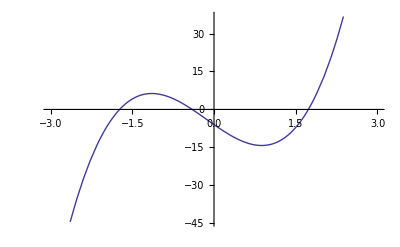

4+30 x

derF= -15+4 x+15 x^2

derF≠0 - True

B=0.0754717

η=0.103774

K=49.

h = 0.383766

True

True

x1 = -0.4

derF≠0 - True

B=0.0417755

η=0.017624

K=94

h = 0.0692076

True

True

x2 = -1.73205

derF≠0 - True

B=0.0263591

η=0.01771

K=94

h = 0.0438812

True

True

x3 = 1.73205

```mathematica
Clear[x];
f=5 x^3 + 2 x^2-15 x-6;
Plot[f,{x,-3,3}]
derF = D[f,x];
Print[D[derF,x]];
Print["derF= ",derF];
(*roots = Solve[derF ==0,x];
root1 = N[x/.roots[[1]]];
root2= N[x/.roots[[2]]];
Print["root1 = ",root1," root2 = ", root2];*)
ckeckKantorovichTheorem[f_,segm_]:=(
Clear[x];
delta = Abs[segm[[2]]-segm[[1]]]/2;
x0=segm[[2]]-delta;
derF1=D[f,x];
derF2 = D[derF1,x]; 
x=x0;
Print["derF≠0 - ",derF1≠0];
B=Abs[1/derF1];
Print["B=",B];
η=Abs[f/derF1];
Print["η=",η];
Clear[x];
K=4 + 30*Max[Abs[segm[[1]]],Abs[segm[[2]]]];
Print["K=",K];
h = B K η;
Print["h = " , h];
Print[h≤1/2];
a = (1 - Sqrt[1 - 2 h])/h*η;
Print[a≤delta];
Return[x0];
);

defineRoot[f_, start_, end_] := (
Clear[x];
x00 = ckeckKantorovichTheorem[f,{start,end}];
xn = x00;
While[Abs[xn - x00] > 0.5 * 10^(-3)  || xn == x00, 
	Clear[x];
         x00 = xn;
          x = x00;
	xn = x00 - f/derF;
         
];
Return[xn];
);
x1 = defineRoot[f,-1.5, 0.5];
Print["x1 = ", x1];
Clear[x];
x2 = defineRoot[f, -3, -0.5];
Print["x2 = ", x2];
Clear[x];
x3 = defineRoot[f, 0.5, 3];
Print["x3 = ", x3];
```

```mathematica
defineRoot2[f_, start_, end_] := (
Clear[x];
x01 = start;
x02 = end;
xn = x01;
While[Abs[xn - x01] > 0.5 * 10^(-3) || xn == x01, 
	
          x = x01;
          fx01 = f;
	x = x02;
	fx02 = f;
	
	xn = x02  - ((x02-x01)fx02)/(fx02 - fx01);
	x01 = x02;
         x02 = xn;         
];
Return[xn];
);
Clear[x];
x1 = defineRoot2[f,-1.5, 0.5];
Print["x1 = ", x1];
Clear[x];
x2 = defineRoot2[f, -3, -1.5];
Print["x2 = ", x2];
Clear[x];
x3 = defineRoot2[f, 0.5, 3];
Print["x3 = ", x3];
```

x1 = -0.4

x2 = -1.73205

x3 = 1.73205